# 2D First-Passage time

## Drift towards the equilibrium at (x~, y~) = (0, 0) with an absorbing boundary at x~=x~*.

## Write down the nondimensionalized Fokker-Planck equation

```mathematica
FP=λt*D[yt*P[xt, yt], xt]+D[yt*P[xt, yt], yt]-κt*D[xt*P[xt, yt],yt]+(1/2)D[P[xt, yt],{xt,2}]+(1/2)*D[P[xt, yt],{yt,2}];
```

## Get the steady-state variances

```mathematica
A= {{ 0,λt},{-κt, 1}}
B = {{1,0},{0,1}}
s=Array[Y,{2,2}]
ss =( s/. Expand[FullSimplify[Solve[A.s+s.Transpose[A]==B.Transpose[B], Flatten[s]]]])[[1]]
```

{{0,λt},{-κt,1}}

{{1,0},{0,1}}

{{Y[1,1],Y[1,2]},{Y[2,1],Y[2,2]}}

{{1/2+1/(2 κt λt)+λt/(2 κt),1/(2 λt)},{1/(2 λt),1/2+κt/(2 λt)}}

## Get the trajectory of the mean (eigenvector)

```mathematica
eig=FullSimplify[Eigenvectors[A]]
```

{{(1+√(1-4 κt λt))/(2 κt),1},{-(-1+√(1-4 κt λt))/(2 κt),1}}

## Choose the parameter values

```mathematica
λts = {0.05, 0.1, 0.2, 0.5};
κts = {0.2, 0.5,2, 5};
κScale = Flatten[Table[κts^2, 4]]
params = Flatten[Table[{λt->l, κt->k}, {l, λts}, {k, κts}], 1]
legend =  Flatten[Table["λt="<>ToString[l]<>"; "<> "κt="<>ToString[k], {l, λts},{k, κts}], 1];
cstar = Flatten[Table[Re[2*κt/(1+Sqrt[1-4*κt*λt])]/.p, {p, params}]];
products = Table[i*j, {i, λts}, {j, κts}]
```

{0.04,0.25,4,25,0.04,0.25,4,25,0.04,0.25,4,25,0.04,0.25,4,25}

{{λt→0.05,κt→0.2},{λt→0.05,κt→0.5},{λt→0.05,κt→2},{λt→0.05,κt→5},{λt→0.1,κt→0.2},{λt→0.1,κt→0.5},{λt→0.1,κt→2},{λt→0.1,κt→5},{λt→0.2,κt→0.2},{λt→0.2,κt→0.5},{λt→0.2,κt→2},{λt→0.2,κt→5},{λt→0.5,κt→0.2},{λt→0.5,κt→0.5},{λt→0.5,κt→2},{λt→0.5,κt→5}}

{{0.01,0.025,0.1,0.25},{0.02,0.05,0.2,0.5},{0.04,0.1,0.4,1.},{0.1,0.25,1.,2.5}}

## Set up the mesh, boundary conditions, and initial condition

#### Steady-state distribution widths in x~, y~

```mathematica
xtwidths = Table[ss[[1,1]]/.p, {p, params}]
ytwidths = Table[ss[[2,2]]/.p, {p, params}]
xywidths = Table[ss[[1,2]]/.p, {p, params}]
```

{50.625,20.55,5.5125,2.505,25.75,10.6,3.025,1.51,13.5,5.7,1.8,1.02,6.75,3.,1.125,0.75}

{2.5,5.5,20.5,50.5,1.5,3.,10.5,25.5,1.,1.75,5.5,13.,0.7,1.,2.5,5.5}

{10.,10.,10.,10.,5.,5.,5.,5.,2.5,2.5,2.5,2.5,1.,1.,1.,1.}

Choose the widest distribution

```mathematica
xtvarChoice=1;
ytvarChoice=4;
xyvarChoice = 1;
```

Initial stds in x~, y~

```mathematica
xtStds = Table[Sqrt[xtwidths[[xtvarChoice]]],Length[params]]
ytStds = Table[Sqrt[ytwidths[[ytvarChoice]]],Length[params]]
```

{4.14508,4.14508,4.14508,4.14508,4.14508,4.14508,4.14508,4.14508,4.14508,4.14508,4.14508,4.14508,4.14508,4.14508,4.14508,4.14508}

{1.78326,1.78326,1.78326,1.78326,1.78326,1.78326,1.78326,1.78326,1.78326,1.78326,1.78326,1.78326,1.78326,1.78326,1.78326,1.78326}

#### Boundary condition at x~* -> y~* = c* x~*. Choose the boundaries to be far enough away from the initial condition and the final distribution

```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
xt0 = 25;
xtls=-5*xtStds
xtrs = xt0+5*xtStds
ytls=cstar
ytrs = cstar*xt0+5*ytStds
```

{-20.7254,-20.7254,-20.7254,-20.7254,-20.7254,-20.7254,-20.7254,-20.7254,-20.7254,-20.7254,-20.7254,-20.7254,-20.7254,-20.7254,-20.7254,-20.7254}

{45.7254,45.7254,45.7254,45.7254,45.7254,45.7254,45.7254,45.7254,45.7254,45.7254,45.7254,45.7254,45.7254,45.7254,45.7254,45.7254}

{0.309584,0.417424,0.527864,0.641101,0.320551,0.438447,0.563508,0.697224,0.333333,0.464816,0.612574,0.78475,0.348612,0.5,0.690983,1.}

{16.6559,19.3519,22.1129,24.9438,16.93,19.8775,23.004,26.3469,17.2496,20.5367,24.2306,28.535,17.6316,21.4163,26.1909,33.9163}

```mathematica
icPos =Table[{xt0, c*xt0}, {c, cstar}];
icVar ={{xtwidths[[xtvarChoice]], xywidths[[xyvarChoice]]},{xywidths[[xyvarChoice]], ytwidths[[ytvarChoice]]}}
ic0 = N[Table[PDF[MultinormalDistribution[pos,icVar], {xt, yt}], {pos, icPos}]];
bcFunc[xtl_, xtr_, ytl_, ytr_] :={
	  P[xtl, yt]==0,
           P[xtr, yt]==0,
           P[xt, ytr]==0,
           P[xt, ytl]==0
};
ΩFunc[xtl_, xtr_, ytl_, ytr_] :=ImplicitRegion[True,{{xt,xtl,xtr},{yt,ytl,ytr}}];
bcs = MapThread[bcFunc, {xtls, xtrs, ytls, ytrs}];
cellDistances = Table[Min[ytStds]/200, 16]
Ω=MapThread[ΩFunc,{xtls, xtrs, ytls, ytrs}];
```

{{17.1817,5.},{5.,3.18}}

{0.00891628,0.00891628,0.00891628,0.00891628,0.00891628,0.00891628,0.00891628,0.00891628,0.00891628,0.00891628,0.00891628,0.00891628,0.00891628,0.00891628,0.00891628,0.00891628}

```mathematica
ytCheckFunc[ytl_, c_]:=c≤ ytl
```

```mathematica
MapThread[ytCheckFunc, {cstar*xt0-5*ytStds, cstar}]
```

{False,True,True,True,False,True,True,True,False,True,True,True,False,True,True,True}

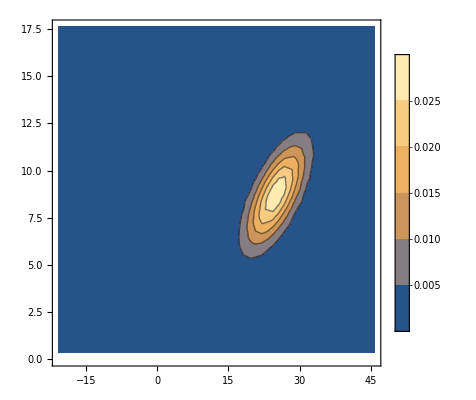

```mathematica
toPlot=13;
ContourPlot[ic0[[toPlot]], {xt, xtls[[toPlot]], xtrs[[toPlot]]}, {yt, ytls[[toPlot]], ytrs[[toPlot]]}, PlotRange->{0, 0.05}, PlotLegends->Automatic]
```

## Calculate the time-integrated probability distribution and the flux through the boundary

```mathematica
NDSolverParams[param_, ic_, bc_, reg_, cell_] :=Module[{N},
N = NDSolve[Join[{(FP/. param)==-ic}, bc],
                                   P,{xt, yt}∈reg, 
Method->{"FiniteElement", "MeshOptions"->{"MaxCellMeasure"->cell}}];
Return[(P/.N[[1]])];
]
```

```mathematica
solsIc0=MapThread[NDSolverParams, {params, ic0, bcs, Ω, cellDistances}];
```

```mathematica
solsIc0[[1]]["ElementMesh"]["Wireframe"]
```

-Graphics-

```mathematica
fluxXIc0 = Table[Derivative[0,1][sol],{sol, solsIc0}];
```

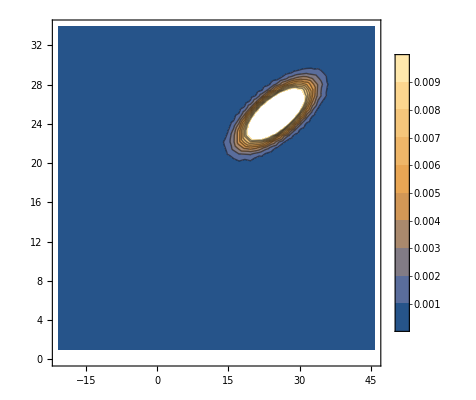

```mathematica
toPlot=16;
ContourPlot[ic0[[toPlot]], {xt, xtls[[toPlot]], xtrs[[toPlot]]}, {yt, ytls[[toPlot]], ytrs[[toPlot]]}, PlotRange->{0, 0.01}, PlotLegends->Automatic]
```

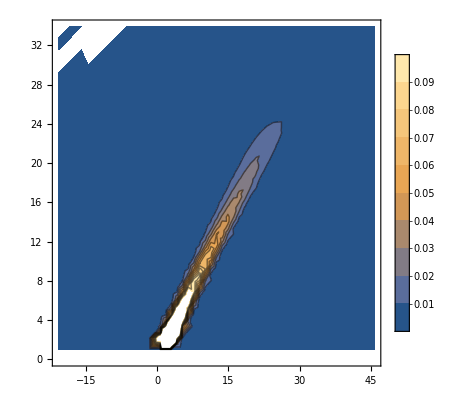

```mathematica
toShow = 16;cIc0 =ContourPlot[solsIc0[[toShow]][xt, yt], {xt, xtls[[toShow]], xtrs[[toShow]]}, {yt, ytls[[toShow]], ytrs[[toShow]]}, PlotLegends->Automatic, PlotRange->{0,0.1}];
(*Show[cSS]*)
Show[cIc0]
```

```mathematica
XIc0 =(MapThread[#1[xt,#2]&,{fluxXIc0,ytls}])*κScale/2;
```

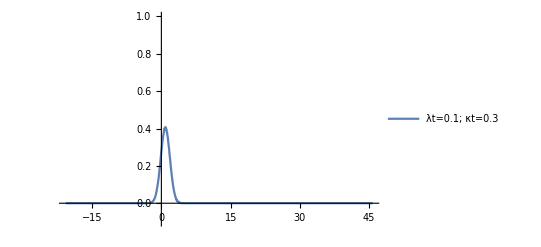

```mathematica
Plot[XIc0[[10]], {xt, xtls[[10]], xtrs[[10]]}, PlotRange->{-0.1, 1}, PlotLegends->legend]
```

```mathematica
IntegFunc[f_, l_, r_] := NIntegrate[f, {xt, l, r}, WorkingPrecision->10]
```

```mathematica
normsIc0 = MapThread[IntegFunc, {XIc0, xtls, xtrs}]
corrected = MapThread[#1/#2&, {XIc0, normsIc0}];
meansIc0= MapThread[IntegFunc, {corrected*xt, xtls, xtrs}]
secondIc0 = MapThread[IntegFunc, {corrected*xt*xt, xtls, xtrs}]
varsIc0 = secondIc0-meansIc0^2
diffIc0 = varsIc0/meansIc0;
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.465569366}. NIntegrate obtained 1.00050819 and 0.001717367733 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.20599603}. NIntegrate obtained 1.000925995 and 0.001342676974 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {0.9464226944}. NIntegrate obtained 0.9995722329 and 0.000635616143 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{1.00050819,1.000925995,0.9995722329,0.9998809994,1.000017217,1.000758201,0.9988065595,0.9996331217,0.9990772176,0.9995087355,0.9979610322,0.9977884093,0.9976162542,0.9960166659,0.9963325237,0.9916114286}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.465569366}. NIntegrate obtained 0.957162537 and 0.001970686248 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.465569366}. NIntegrate obtained 0.9474412008 and 0.001356494507 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {2.763436046}. NIntegrate obtained 0.9337450045 and 0.001016306629 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{0.957162537,0.9474412008,0.9337450045,0.9212460865,0.9237550773,0.900184174,0.872625634,0.8477603255,0.8932179872,0.8532392905,0.8170120604,0.7792639054,0.8600111279,0.8105997727,0.7637158327,0.7100094969}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.465569366}. NIntegrate obtained 1.846504382 and 0.002164430683 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {3.15279605}. NIntegrate obtained 1.865084112 and 0.00336619688 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {3.023009382}. NIntegrate obtained 1.854226128 and 0.002561877648 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{1.846504382,1.865084112,1.854226128,1.837083523,1.796758521,1.777980529,1.750305931,1.710296248,1.742519386,1.701952401,1.657344352,1.60749465,1.687109889,1.641851417,1.585395949,1.562343305}

{0.93034426,0.967439283,0.982346394,0.988389171,0.943435078,0.967648981,0.988830434,0.991598679,0.944681014,0.973935114,0.989835645,1.00024242,0.947490748,0.984779425,1.00213408,1.05822982}

```mathematica
grid = Flatten[Table[{l, s}, {l, λts}, {s, κts}], 1];
params
```

{{λt→0.1,κt→0.3},{λt→0.1,κt→0.4},{λt→0.1,κt→0.5},{λt→0.1,κt→0.6},{λt→0.2,κt→0.3},{λt→0.2,κt→0.4},{λt→0.2,κt→0.5},{λt→0.2,κt→0.6},{λt→0.3,κt→0.3},{λt→0.3,κt→0.4},{λt→0.3,κt→0.5},{λt→0.3,κt→0.6},{λt→0.4,κt→0.3},{λt→0.4,κt→0.4},{λt→0.4,κt→0.5},{λt→0.4,κt→0.6}}

```mathematica
normArrayIc0 = ArrayReshape[normsIc0, {4,4}];
varArrayIc0 = ArrayReshape[varsIc0, {4,4}];
meanArrayIc0 = ArrayReshape[meansIc0, {4,4}];
diffArrayIc0 = ArrayReshape[diffIc0, {4,4}];
```

```mathematica
cf[x_]:=Blend[{{-2, Red},{ 1,White},{5,Blue}}, x]
```

```mathematica
xticks = Transpose[{{1, 2, 3, 4}, λts}];
yticks = Transpose[{{1, 2, 3, 4}, κts}];
```

```mathematica
varArrayIc0
```

{{0.93034426,0.967439283,0.982346394,0.988389171},{0.943435078,0.967648981,0.988830434,0.991598679},{0.944681014,0.973935114,0.989835645,1.00024242},{0.947490748,0.984779425,1.00213408,1.05822982}}

```mathematica
ArrayPlot[varArrayIc0, ColorFunction->(Blend[{{-1, Red},{ 0,White},{1,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->"Var("OverTilde[xt]   .")"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λt, κt}]

ArrayPlot[ArrayReshape[Table[Blend[{{-2, Red},{ 0,White},{5,Blue}}, i],{i,Flatten[meanArrayIc0]}], {4,4}], PlotLegends->{Placed[BarLegend[{cf[#]&,{-2, 5}},LegendLabel->"mean(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λt, κt}]

ArrayPlot[normArrayIc0, ColorFunction->(Blend[{White,Blue},#]&), PlotLegends->{Placed[BarLegend[Automatic,Automatic,LegendLabel->"norm(e(x))"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λt, κt}]
```

-Graphics-

-Graphics-

-Graphics-

#### Check that all s.s. variances have been reached before mean passage

```mathematica
S[A_, B_] := FullSimplify[Integrate[MatrixExp[-A*(t-tp)].B.Transpose[B].MatrixExp[-Transpose[A]*(t-tp)], {tp, 0, t}]];
```

```mathematica
As = {{ 0,λ},{-κ, 1}}
Bs = {{Sqrt[2*λ],0},{0,Sqrt[2] }}
s0[λ_, κ_, t_] = FullSimplify[MatrixExp[-{{ 0,λ},{-κ, 1}}*t].icVar.MatrixExp[-Transpose[{{ 0,λ},{-κ, 1}}]*t]]
```

{{0,λ},{-κ,1}}

{{√2 √λ,0},{0,√2}}

{{1/(-0.25+1. κ λ)(ⅇ^-t (-0.5+1.03 κ+0.75 λ) λ+ⅇ^(-t (1+√(1-4 κ λ))) (-0.2575+0.2575 √(1-4 κ λ)+λ (0.25+0.515 κ-0.375 λ-0.25 √(1-4 κ λ)))+ⅇ^(t (-1+√(1-4 κ λ))) (-0.2575-0.2575 √(1-4 κ λ)+λ (0.25+0.515 κ-0.375 λ+0.25 √(1-4 κ λ)))),1/(-0.25+1. κ λ)(-0.2575 Cosh[t]+0.2575 Sinh[t]) (0.970874-2. κ-1.45631 λ+(κ (2.-3.8835 λ)+1.45631 λ) Cosh[t √(1-4 κ λ)]+2. (1. κ-0.728155 λ) √(1-4 κ λ) Sinh[t √(1-4 κ λ)])},{1/(-0.25+1. κ λ)(-0.2575 Cosh[t]+0.2575 Sinh[t]) (0.970874-2. κ-1.45631 λ+(κ (2.-3.8835 λ)+1.45631 λ) Cosh[t √(1-4 κ λ)]+2. (1. κ-0.728155 λ) √(1-4 κ λ) Sinh[t √(1-4 κ λ)]),1/(-0.25+1. κ λ)(ⅇ^-t κ (-0.5+1.03 κ+0.75 λ)+ⅇ^(t (-1+√(1-4 κ λ))) (-0.1875+0.1875 √(1-4 κ λ)+κ (0.25-0.515 κ+0.375 λ-0.25 √(1-4 κ λ)))+ⅇ^(-t (1+√(1-4 κ λ))) (-0.1875-0.1875 √(1-4 κ λ)+κ (0.25-0.515 κ+0.375 λ+0.25 √(1-4 κ λ))))}}

```mathematica
curve =S[As, Bs]
```

{{(λ (-((-1+ⅇ^(t (-1+√(1-4 κ λ)))) (1-2 (-1+κ) λ+√(1-4 κ λ)))/(-1+√(1-4 κ λ))+((1-ⅇ^(-t (1+√(1-4 κ λ)))) (-1+2 (-1+κ) λ+√(1-4 κ λ)))/(1+√(1-4 κ λ))+4 (1+κ) λ (1-Cosh[t]+Sinh[t])))/(-1+4 κ λ),-(ⅇ^(-t (2+√(1-4 κ λ))) (4 ⅇ^(t (1+√(1-4 κ λ))) (1+κ) λ+ⅇ^(t (2+√(1-4 κ λ))) (2-8 κ λ)-ⅇ^(t+2 t √(1-4 κ λ)) (1-2 (-1+κ) λ+√(1-4 κ λ))+ⅇ^t (-1+2 (-1+κ) λ+√(1-4 κ λ))))/(2 (-1+4 κ λ))},{-(ⅇ^(-t (2+√(1-4 κ λ))) (4 ⅇ^(t (1+√(1-4 κ λ))) (1+κ) λ+ⅇ^(t (2+√(1-4 κ λ))) (2-8 κ λ)-ⅇ^(t+2 t √(1-4 κ λ)) (1-2 (-1+κ) λ+√(1-4 κ λ))+ⅇ^t (-1+2 (-1+κ) λ+√(1-4 κ λ))))/(2 (-1+4 κ λ)),(-((1-ⅇ^(-t (1+√(1-4 κ λ)))) (1+2 (-1+κ) κ λ+√(1-4 κ λ)))/(1+√(1-4 κ λ))+1/2 (-1+ⅇ^(t (-1+√(1-4 κ λ)))) (1+κ-√(1-4 κ λ)+κ √(1-4 κ λ))+4 κ (1+κ) λ (1-Cosh[t]+Sinh[t]))/(-1+4 κ λ)}}

```mathematica
toPlotCurve[λ_, κ_, t_]=(s0+(λ (-((-1+ⅇ^(t (-1+√(1-4 κ λ)))) (1-2 (-1+κ) λ+√(1-4 κ λ)))/(-1+√(1-4 κ λ))+((1-ⅇ^(-t (1+√(1-4 κ λ)))) (-1+2 (-1+κ) λ+√(1-4 κ λ)))/(1+√(1-4 κ λ))+4 (1+κ) λ (1-Cosh[t]+Sinh[t])))/(-1+4 κ λ))[[1,1]]
```

1/(-0.25+1. κ λ)(ⅇ^-t (-0.5+1.03 κ+0.75 λ) λ+ⅇ^(-t (1+√(1-4 κ λ))) (-0.2575+0.2575 √(1-4 κ λ)+λ (0.25+0.515 κ-0.375 λ-0.25 √(1-4 κ λ)))+ⅇ^(t (-1+√(1-4 κ λ))) (-0.2575-0.2575 √(1-4 κ λ)+λ (0.25+0.515 κ-0.375 λ+0.25 √(1-4 κ λ))))+(λ (-((-1+ⅇ^(t (-1+√(1-4 κ λ)))) (1-2 (-1+κ) λ+√(1-4 κ λ)))/(-1+√(1-4 κ λ))+((1-ⅇ^(-t (1+√(1-4 κ λ)))) (-1+2 (-1+κ) λ+√(1-4 κ λ)))/(1+√(1-4 κ λ))+4 (1+κ) λ (1-Cosh[t]+Sinh[t])))/(-1+4 κ λ)

```mathematica
Manipulate[Plot[{toPlotCurve[λ, κ, t],  1/κ+((1+κ) λ)/κ}, {t, 0, 30}, PlotRange->{0, 10}, GridLines->{{{tfPlot [λ, κ, 8],Red}},None}], {λ, 0.02, 0.2}, {κ, 0.2, 2}]
```

```mathematica
tfPlot [λ_, κ_, x0_] := (1/λ)*Log[x0/(2*κ/(1+Sqrt[1-4*λ*κ]))]
```